```mathematica
video1coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video1coordinates.csv","CSV"];
video2coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video2coordinates.csv","CSV"];
video3coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video3coordinates.csv","CSV"];
video4coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video4coordinates.csv","CSV"];
video5coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video5coordinates.csv","CSV"];
video6coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video6coordinates.csv","CSV"];
video7coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video7coordinates.csv","CSV"];
video8coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video8coordinates.csv","CSV"];
video9coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video9coordinates.csv","CSV"];
video10coordinates = Import["/Users/blakeduschatko/Desktop/School Work/2016b - Fall/Modern Lab/Lab 2/Coordinate Data/video10coordinates.csv","CSV"];

(*
Features
[
which list (Frame number),
which set of points (which particle), 
x or y coordinate (in pixels)
]
*)
video1coordinates = Drop[video1coordinates,{301}]; (*Drop row 301*)
video1coordinates =Drop[video1coordinates,{},{11}]; (*Drop column 11*)
video2coordinates = Drop[video2coordinates,{},{1}];
video2coordinates = Drop[video2coordinates,{},{2}];
video2coordinates = Drop[video2coordinates,{},{10}];
video3coordinates = Drop[video3coordinates,{},{14}];
video4coordinates = Drop[video4coordinates,{},{2}];
video4coordinates = Drop[video4coordinates,{},{9}];
video6coordinates = Drop[video6coordinates,{},{15}];
video7coordinates = Drop[video7coordinates,{},{1}];
video7coordinates = Drop[video7coordinates,{},{4}];

For[i=1,
i< 301,
i++,
For[j=1,
j<11,
j++,
video1coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video1coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<14,
j++,
video2coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video2coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<14,
j++,
video3coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video3coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<10,
j++,
video4coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video4coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<18,
j++,
video5coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video5coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<15,
j++,
video6coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video6coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<5,
j++,
video7coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video7coordinates[[i,j]],("{"|"}")],","]
]
]


For[i=1,
i< 301,
i++,
For[j=1,
j<4,
j++,
video8coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video8coordinates[[i,j]],("{"|"}")],","]
]
]

For[i=1,
i< 301,
i++,
For[j=1,
j<5,
j++,
video9coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video9coordinates[[i,j]],("{"|"}")],","]
]
]

For[i=1,
i< 301,
i++,
For[j=1,
j<6,
j++,
video10coordinates[[i,j]] = Flatten@ToExpression@StringSplit[StringTrim[video10coordinates[[i,j]],("{"|"}")],","]
]
]
```

```mathematica
v1displacements =Array[0,{300,10}];
v2displacements= Array[0,{300,13}];
v3displacements=Array[0,{300,13}];
v4displacements= Array[0,{300,9}];
v5displacements=Array[0,{300,17}];
v6displacements= Array[0,{300,14}];
v7displacements=Array[0,{300,4}];
v8displacements= Array[0,{300,3}];
v9displacements= Array[0,{300,4}];
v10displacements= Array[0,{300,5}];


For[i=1,
i<301,
i++,
For[j=1,
j<11,
j++,
v1displacements[[i,j]] = (video1coordinates[[i,j,1]]-video1coordinates[[1,j,1]])^2+(video1coordinates[[i,j,2]]-video1coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<14,
j++,
v2displacements[[i,j]] = (video2coordinates[[i,j,1]]-video2coordinates[[1,j,1]])^2+(video2coordinates[[i,j,2]]-video2coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<14,
j++,
v3displacements[[i,j]] = (video3coordinates[[i,j,1]]-video3coordinates[[1,j,1]])^2+(video3coordinates[[i,j,2]]-video3coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<10,
j++,
v4displacements[[i,j]] = (video4coordinates[[i,j,1]]-video4coordinates[[1,j,1]])^2+(video4coordinates[[i,j,2]]-video4coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<18,
j++,
v5displacements[[i,j]] = (video5coordinates[[i,j,1]]-video5coordinates[[1,j,1]])^2+(video5coordinates[[i,j,2]]-video5coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<15,
j++,
v6displacements[[i,j]] = (video6coordinates[[i,j,1]]-video6coordinates[[1,j,1]])^2+(video6coordinates[[i,j,2]]-video6coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<5,
j++,
v7displacements[[i,j]] = (video7coordinates[[i,j,1]]-video7coordinates[[1,j,1]])^2+(video7coordinates[[i,j,2]]-video7coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<4,
j++,
v8displacements[[i,j]] = (video8coordinates[[i,j,1]]-video8coordinates[[1,j,1]])^2+(video8coordinates[[i,j,2]]-video8coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<5,
j++,
v9displacements[[i,j]] = (video9coordinates[[i,j,1]]-video9coordinates[[1,j,1]])^2+(video9coordinates[[i,j,2]]-video9coordinates[[1,j,2]])^2
]
]

For[i=1,
i<301,
i++,
For[j=1,
j<6,
j++,
v10displacements[[i,j]] = (video10coordinates[[i,j,1]]-video10coordinates[[1,j,1]])^2+(video10coordinates[[i,j,2]]-video10coordinates[[1,j,2]])^2
]
]

(*300 frames, 92 particles*)
alldisplacements = Join[v1displacements,v2displacements,v3displacements,v4displacements,v5displacements,v6displacements,v7displacements,v8displacements,v9displacements,v10displacements,2];
```

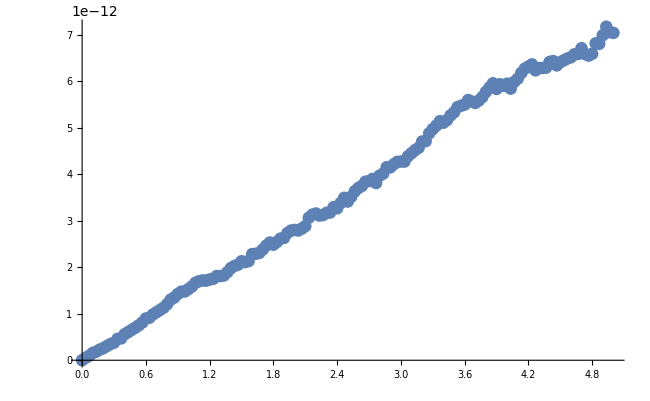

FittedModel[-2.18433×10^-14+1.457×10^-12 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.18433×10^-14 | 2.27662×10^-14 | -0.959462 | 0.338881
x | 1.457×10^-12 | 7.87333×10^-15 | 185.055 | 5.61902×10^-178

```mathematica
(*Frame,R^2*)
averagedisplacements = 
Table[
(1/92)*Sum[alldisplacements[[i,j]],{j,1,92}],
{i,1,300}
];
adjusteddisplacement = Table[((.1099*10^(-6)))^2*averagedisplacements[[i]],{i,1,300}];

testaverageddisplacements = Table[
(1/92)*Sum[alldisplacements[[i,j]],{j,1,92}],
{i,1,151}
];
testadjusted = Table[((.12*10^(-6)))^2*testaverageddisplacements[[i]],{i,1,151}];

timesteps = Table[i/30,{i,0,299}];
testtimesteps = Table[i/30,{i,0,150}];

datapoints = Flatten[{timesteps,adjusteddisplacement},{{2},{1}}];
testdata =  Flatten[{testtimesteps,testadjusted},{{2},{1}}];

(*adjusteddatapoints =Flatten[{timesteps,averagedisplacements},{{2},{1}}];*)


ListPlot[testdata]
lm = LinearModelFit[testdata,x,x]
lm["ParameterTable"]
```